```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["y[2].txt", "Data"];
```

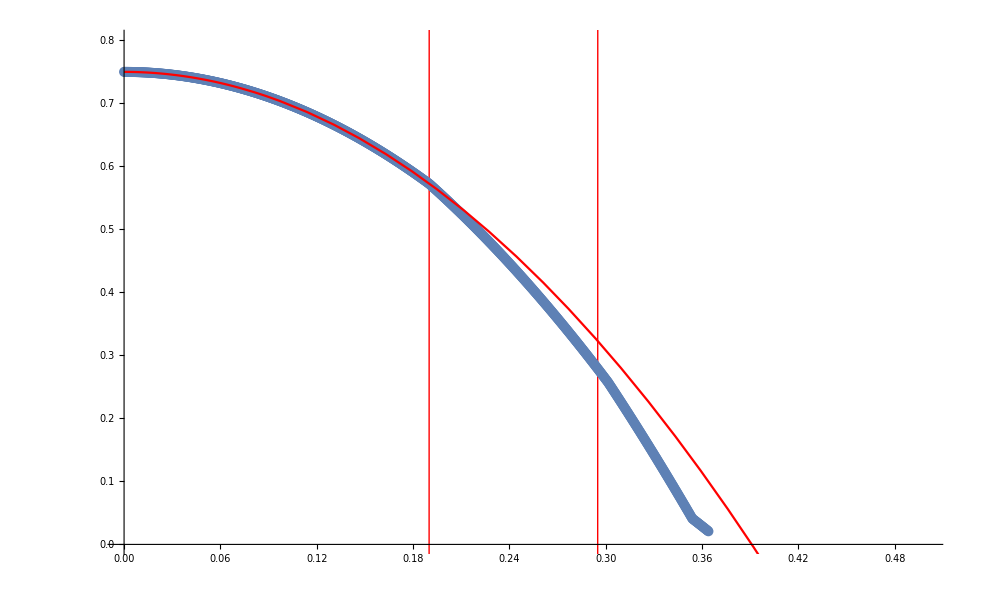

```mathematica
dt = 0.0001;
(*ListPlot[data, Joined -> True]*)
Show[Plot[1000*Sign[x-0.190034],{x,-100, 100},ExclusionsStyle->Red],
Plot[1000*Sign[x-0.295053],{x,-100, 100},ExclusionsStyle->Red],
ListPlot[data],Plot[data[[1]][[2]]-0.5*9.81*t *t,{t, 0, 0.8}, PlotStyle -> {Red}], PlotRange ->{ {0, 0.5},{0, 0.8}}]
```

```mathematica
data2 = Import["ydot[2].txt", "Data"];
```

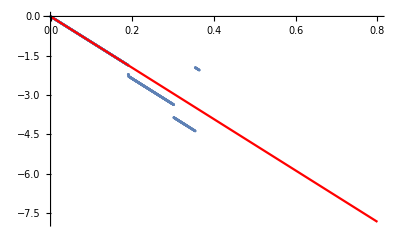

```mathematica
Show[
ListPlot[data2],Plot[-9.81*t,{t, 0, 0.8}, PlotStyle -> {Red}], PlotRange -> {{0, 0.8},{0, -7}}]
```

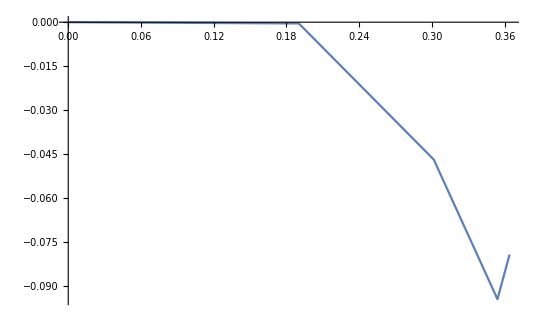

```mathematica
aaa = {};
For[i = 1, i ≤ Length[data], i++, aaa = Append[aaa, {data[[i]][[1]], data[[i]][[2]] - (data[[1]][[2]]  - 0.5*9.81*data[[i]][[1]]*data[[i]][[1]])}]];
aaa;
ListPlot[aaa, Joined -> True]
```